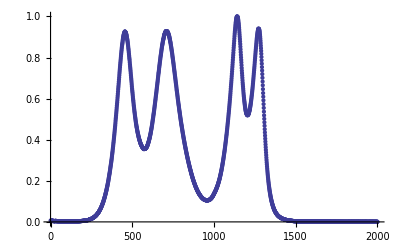

```mathematica
(*通过实验测得的Red LED光谱数据*)
redSpd=Import["D:\\smartLighting\\smartLighting\\data\\redSpdData.xls"]//Flatten[#,1]&;
(*redSpd[[All,1]]=redSpd[[All,1]]*10^-9;*)
maxRedSpd=Max[redSpd[[All,2]]] ;   (*相对光谱峰值大小，应该为1*)
redSpd⟦All,2⟧=redSpd[[All,2]]/maxRedSpd;  (*归一化*)


(*通过实验测得的Amber LED光谱数据*)
amberSpd=Import["D:\\smartLighting\\smartLighting\\data\\amberSpdData.xls"]//Flatten[#,1]&;
maxAmberSpd=Max[amberSpd[[All,2]]] ;   (*相对光谱峰值大小，应该为1*)
amberSpd[[All,2]]=amberSpd[[All,2]]/maxAmberSpd;   (* 归一化*)

(*通过实验测得的Red LED光谱数据*)
greenSpd=Import["D:\\smartLighting\\smartLighting\\data\\greenSpdData.xls"]//Flatten[#,1]&;
maxGreenSpd=Max[greenSpd[[All,2]]];    (*相对光谱峰值大小，应该为1*)
greenSpd[[All,2]]=greenSpd[[All,2]]/maxGreenSpd; (*归一化*)

(*通过实验测得的Red LED光谱数据*)
blueSpd=Import["D:\\smartLighting\\smartLighting\\data\\blueSpdData.xls"]//Flatten[#,1]&;

maxBlueSpd=Max[blueSpd[[All,2]]];    (*相对光谱峰值大小，应该为1*)
blueSpd[[All,2]]=blueSpd[[All,2]]/maxBlueSpd;  (*归一化*)

ragbLedSpd[kr_,ka_,kg_,kb_]:=kr*redSpd⟦All,2⟧+ka*amberSpd⟦All,2⟧+kg*greenSpd⟦All,2⟧+kb*blueSpd⟦All,2⟧;
nRagbLedSpd[kr_,ka_,kg_,kb_]:=ragbLedSpd[kr,ka,kg,kb]/Max[ragbLedSpd[kr,ka,kg,kb]]
nRagbLedSpd[1,1,1,1];
ListPlot[nRagbLedSpd[1,1,1,1]]
```

```mathematica
spdDataFromXls=Import["D:\\smartLighting\\smartLighting\\data\\wLED3583Spd.xls"]//Flatten[#,1]&;
spdDataWaveLength=spdDataFromXls[[All,1]];
spdData=(*spdDataFromXls[[All,2]]*)nRagbLedSpd[1,1,1,1];
(*spdDataFromXls[[All,2]]*)
```

```mathematica
cie1931Table="1:eJyFmnk01N//xyWVLMUHrRSlUloQpWJeFy2K7JWK7CItlH2dYTC0WCrJTkJZI0Ipkp3sS0r2fRuUSPjp435+58z88fX+o3M6j05m3s/7uPf1el0C+rfUjBgZGBi4Fv5gYsBP7m3E8L+eqiV42xKcugRnuPO/OccSnH8JLrIER0twlSW47hLcfAlOXIL7LsEjluApS/DcJXjVErxtCU5dgjNY/m/OsQTnX4KLLMHRElxlCa67BDdfghOX4L5L8IgleMoSPHcJXrUEb1uCU5fgDFb/m3MswfmX4CJLcLQEV1mC6y7BzZfgxCW47xI8YgmesgTPXYJXLcHbluDUJTiD9f/mHEtw/iW4yBIcLcFVluC6S3DzJTjRGiXd6CZmrhQA7uixj003qggce8obzn2Tg3+5rzW69CxXpIpvOxxJMb3of6OG4K+fNx6hfHKRR1ijXSoS6qdtd0D2aMHRrYl1BGOBf16S/jm9yFOskdZFkw/btwhBdQx1kke8kcBmPuCrtF9xkedao+PRzoo664Uhx0XMkJ2lmbBa0/rYlQTlRV5ljXauC62eMdsPH73FwkMOtRBujVHDlpepLvI2a9RWlXzszDpRCBkmRafotxEeNQxJuc6rL3KqNXprp+w9I34Q7suxOw7rdxBSZdW8o53OL3IGG8RYwJZyKEACVPyefMuK6iK8Wp6lIX3m4iLnsEFc4ycp/ARJGBvRmy4R6iXY9Waabr2mtcj5bdBZpD3SInIM4qX3R9XN9BPG3vYH8HXoLHIRG6R/r/jWGTMCbFtlFiexdZjARSzcKtCot8iRDVr9qHbcb5kMMPZsEuRXoRKuqlfPy/4wWOQqNkiOeG5ijEMO2KQdeZTPjBPMDspsVNMzXuS6NihXpqSCZHsCLpBvs09TfhC4pdtXCh82XeTmNihJ+VHrrKI8FKSmto2v+0XYGF8xH//g+iIn2iCVPhKEpyiAzXLu3EbW34RtJZqt6vLmOH8b9NV4wnN1sDKUzTdkHL86S9h+xV3U6ultnL8NKg3Q8LpHVYULZ4flV1IYoChSaqaT3wrnb4OKlZ571wtrAGvnD2OSNSM8twj4U/LJBudvgy6zplV9Nj0P5KyWMqfbTKAR//Knipk9zt8GXVvL38ceognnK8V71lquhHfF/Kpnljvh/G2QZ9Uuuet9l0B0S5peQSAzxJReD3qb5YLzt0FCNxJG33lqQ+qGR0LSbKwwPXxXid2UhPO3RVu6rNuvXtQFa1GuHet+s4N//KvXI6fccP626FvE5OVjqvpwfzg94lchBxzTPpByLNgd52+LnCzYrNYVGMKNIAMO6uQ/MLZN28mDRMH52yKfEwKmR1OvQoXaWU/h+zwwtc+gKfjXXZy/LbIMvsh1gcUMbq/88uOI2wY4V/cyNmLIB+dvizgOTh/b/OEmvHqmpJJQsxlyv4Qcad7lj/O3RUxWpc8261mAKd+5sxxWWyFpI9Vw1vMRzt8WXWxfz5FNugMa4fxvlV8JQKH4j7LD7E9w/gvf76VXy886K/BJW6Vz9Ot2qC+wel78+SnO3xa5zYjKb3OyhVOjpwKOKe8E53mhjss/Q3D+tmhg79cq/xAH0LEu6TopuBuyT5xaW6kRgfO3RQrFq6SDz7lA1nXLz8oWeyHd6+EMn3cUzt8W8bJEG0sPkcBaPOKgyX4RaKj2rlE7/Bznb4syfIYcV3iToXmTWND1m2LAdizxgolaHM7fFpXnvgmXNfSEz22JM22t4jCfpF7/ND0e52+LArNi5Tkve4PIXEsp1fQwlH2lwrZjyTh/O9RTxprio3QfrM2eshVNHIGiNzMnwq68wvnbIVddRqsabl947Vdyx+O6FNgSjLm9ONNw/nbIUZtFcqOPH9Q+OhyykgEgeu6iDW/da5y/Hao7+ea8/rGH8IfYKi07heDQgy1tBTUZOH87VP8lQu8X4TGYT2w/uyVXFloiRgbGj2Th/O3QHaLugy0fnsCYSSclfeo4KAwwiXMeeofzt0O8YCW0qSEIKO9cc9nen4JZrx0orucDzt8OqazUNVZ0CYM8Ne3cMjYFOFAVvVx++0ecvx066PJmZaNmJAgQy9NXNCpBjENo3ZPnn3D+dqh5l+3Y5tRnEFDO3WvsqQoJrvpWPy2LcP526DTnxvNjJ2Pg4LRx8OZadVilE6jIc68U52+HpLIUPCd4XkBt6g6ularnYWfqNbPw/gqcvx1yGOVePyScAH63Ky3MuS+CaNQz1ojPVTh/O3Qif8Op4KfJQDRfzvXhgBZIySTIB7TU4Pzt0FCkU0Lbm1cgvpMI59J14M+hT7YVwvU4fzt0FImc8mlNA+1Yv4DSr3rwXAlx6eU34vzt0cvr/nMdshkg8nImYx2vIRSyHnQWftaM87dHVIFzNf5tmbCJYnTQM9oYmLX5Lu8pbcH52yODvfv73XLfgo3PNgGitykINErNno9sw/nbo+0TN4yfDryHqDUej406r4O5yit+t7sdOH979Pt4mKD2wTz482Ks5qy+OVDdSzTy4rpw/vYot0nUUHhLPjT5DizjDr8NPx5Pvque7cH52yN1roOvkoULYGdixjWqgBVIHZnuTHDux/nbI2ct605JhSI4Pad5y6LNBoKTh+VV1g/h/O0RO29VDc/1EnjuVmexo8oeOiWp17LSRnD+9qgsi/vCY6cyCJfaWxfU4wTsTsbz4+FUnL89OnzyT91H6wqwfFcXGOdDhB8WxXp3m8Zw/gt8p33lYc1KYP1sKPSO4AqdaI7CwzSB87dHIWG8Lz/7VAH/brlqrmVkCL6S031C4AfO3x5xN6lNKhpVg05ttO+xRneQPdtZUbX/J87fHlUa1/deE66BthDO5zl5nrD490mcvz3awFv683JbDUwwxylPfvCC06O5z5l5fuH8HdC2+ywh191qoSvIo1qm+i6ICu7iejOAOYcD6gv+or6epw4qtkmY7pm8D1nnzN5VJkzh/B2Q6R77gIbHdWB54FpD6HpfkPtj0hJ/eRrn74AiNh1oEVxZD6Wza06QCH5gaBXfG/0Lc+SADJdlzjEa10Og6E47d3N/SJz/rBpF/I3zd0C1cs6nwtLrwTqxYehnwkMgqZvWT01iruuASL1uLGk/68HRuOdc69gjKDnKq/388gzO3wEJa7N++rOzAXJVN19Tkg4AdIFT8Hky5kQHVG1pLSZ5pgEuGR5rVb7/BMyMPh74OYG5rwMarFOQbdJpgA6BxMTktkB4v6LYQ3D3H5y/AxLpGHtWZdIABK8pXv8jQWBQ7+Cuq4J5igPKEGEdDjFuAK3mP8tWBQdD9s7Tjg/NMM91QNkf7L+9udQA46MH9/Myh4KAYvDbWEfMqxzQ22HZO6EnG0CsJ2lHl1sYTD5peejpjnmbAzp+enjg954GCIvK5JteFQHk4fIXqz0xpzqgZ2Tl3UbMDaAhoCku0BABRVHHYxpJmDM4IjUWHSaxtnrwSGv0z02IBM4oAUqgDeYcjujwWoucN2n18LP99tZ996LALbE4bMIUc35H9Mz/6LKz5Hr4Ou187Z3lM2CJGlnuewlzEUe0+sHO27zq9WCoxKhXbBwNBoU7mkrOYI4cUY1z+mvDrfWg1b2aHKr/HB50a/8kHsFcxRGJi5y9/rS3DgSdLp1wMYkBNmZmmShBzHUdkU/TQ6N9L+vgUWBNboptLGjaaW/axIK5uSMisysnPzKqg99/P97DOBiX+WvIf/k7osvtsW//bKgDJbdvgt5ZL6Aos6Mj7t1/+TsiPydfo7xPtVDI0evcPPASpPqKiVEUzCMckYGE4nZe01qIOXHM2nRnAihExTmRFTBPcUSRfu/nT6ysBQnknXHULBF2hWkqcq7APNcRvVIxC7IJqYHMLe6DqplJIPJ211rWdLy+qxzRy8Rtw757a0AkuaogaWUKNHh/ZT+lhXmbI2IOLUyoSK8GfT1f9lUZKZD20DjQZRr7RXVEh/5wLZuQqIZAjksJ4mavIPtPR6KSF+YMTsj7dd9U/ssqOHbCLuHorlTgqtnkpsSMOYcTuvls2bsV/1SB/fO9cryDqbBeXuXPhjv/+e+Evhn0y62v+wwdZcc51d6kgcdV9Q+8RXj/EHFCwtvsQvPNKuBg5q/s8/deQ4nkydRTzJgjJ1Q2H6T/6UcZ8FV+nD5glg5KHTmvx6Xw/qXihAa7bYLKbUtBxWq7Z6dGBrh6K8dYm+H9T9cJtQvZWT1YVgKOa5/w2px5A9UXfI33BuH909wJsUvnJCo/KgJPRk5psmIm7LTSVncox/sv0QlZuBILAw4UglZj0B3Oy1kgrhTGrrEMc18nZG5olzpZ8wk4pm3FTltnQ5XyLh9tyXGcvxMaYgvtY3LOB/PJHCn1sLewvNxxFVj8t/87IV5HPbFzIh/h+4K1l2rfAfNCNRgej8+PXCfk85DP+uhgLtR8Opb7cN17yNeRdLSpGsX5O6HrzQ6xmbofIM1iTV/A1Q9w2WNEPl4Fn09tTqg35rZL0Pw7qK1Ye4NTPxd4FqqJ1034fKM6IY0wb6PjadkwGFl0ZIY7Dz4P1LZdNx3E+TsjQRcR6jeHTEhLfy9vUpYHB34GDicvH8D5O6PcEHETuYsZUKSPgvPIH0H0H99urrg+nL8zKtzKu4Vy9jVcjjs5/VA2H6KfrAoPudCL83dGZmzvL27QSgXnyeK7Yys/QfDGqOQCLnx+I2fEe3rusB4lBfIcZudHaj/B40m9Dazf/zv/nZGfLSk+PD4Rv7cCOHV7em3/m06cvzOanEuLjr//Evqj1U5t8ymE0CrfgFtRuL4wd0buCmF8h1JjYZuUxHidcxFMM5+8xRjajvN3Rgw3g65mcz6H+td3TWMciqFO4Nvq4Bhcv/g6o13WjHVp0VFQMcB309OjBLi72K4ZOrbi/J3RwuFxJdQgAs7NWEoZR5RCjkTKOdcCXB+lOKPe0pmH6gEhMFPUm/24tAz27LvhmrXrG87fGbGnecgoZwXCltkDjVErKoBgVuyVG4XrrypnpC1RyTm9/zF8jNmtfU71Mzi5fE/WlviC81/gV26p8k76QdDvA4XWiZXwQnPQXvM7ru+ozmiHFWMQ8+YH0P8meXnvvSpY3G8acP4uiM/HseZUHwXetl4ITj9TDbqtEybKN3H9yLHAH0s6D6iQgWPt+lubOGvgdzwna6FaHc7fBcXJDHzhVyVCcxGL8+aOGqh918nNd7oW5++C3iy3dRUrtQPxX77UnA+1ILvBa1OACq5fkQveXyzBrn+nKHNCHYR84k+5bVKN83dB5Z0HVZTGbsIJy43yenH10KGy+qmVL66PdV1QTqJ5VDG/CWz82MC5N60B5sXnp4vuVeL8XdD5T85eF1oM4Nvy90N9JY1gNOH6lIH9M87fBbnEPHzRtNDf6lorb1k30AShVo3btwSV4/xd0F9797wwgHtn/jYezbDtuu3CVliG83dB31V3P5H9dRUyiveKukt/hRgxB5/+DyU4fxe0SeCczZcbt+AIvzrF79Y3CFv7d8BUjPN3QVSeOcohMSvY5H/6D4prgWVXP4d/pRbi/F3Q3Bx/nfRTR/j1KITLoe87FIa8sjN+WIDzd0GfKTXf21jdwOXv8bahDbq4+Uq6AfcvVBdUov96rK6dAsqcAVe589pgnWMXv9gk7n8YiEjnGx/5ZLUPrB9nvhl9vR3ErhZdUMzIW+TMRHTxZ4T0wNhD0H0oMSCwqQOa6w4Utbvm4vVBRCTJSS8fv0Do1R26Y1bcAa+0fTulc94v8g1EpMUvM2ZQHgoLDjfpWHfCyUeTK3UCcf/GT0S/7muQUW0kHJWQ0n+6vQt0Fspf0tPsRS5ERD1MVSFp7M8hNqtMXKWyCz5XHBA9+CETry8iKnsy99HZLw4CVK2PV9p0g0N/kOfm1W8WuSQRLduRWvH4UgJk8Jx319vcA+8cdNo6rNPx+iMiCYO/FWAKPn97gPPy5IwIM+5f5Yko5IvY6oTzqXCv/AabwtleiHlXs7o2JxWvTyI63Kult/fpazhiW2bf0NwL6bI71bse4f5Zk4gO7tJ8JTadAZwpr2LY9ftAe+Ffkz1T8PolIg81fs3fVllgzCjOwNLVB6ZRlg9ituL+3GTh+0N06/s17+DurNGvLr1+eP74jF+rciJe30TEE8J640z+e2hpsLjA8q0fNl7Larr4FPf/tkQUy/RJUKs4F/RTGe93qg7Aen7tJOuZF3j9ExFxJSLxHvkIJuQb9ivzF3jZn3dsd/B8gUJESusS/Z1f5YO0zCrG1QcGIcBZJ3n8Twz2g4hKrN+HbzpQAH+rfNLjQSD/Y9w89xjPLwKJ6NBwjrpWSiFMevJyyk4OwtugzRcUj0Zjf4gop3C/ao5EMRRzFr4MUR2Ci6kZZkf78XwkjojUtH5LDS74lNKaKdoROwQV+++lekRHYr+IiNDivcZfuQzenr/HZDg9BB7d1IKRG3j+kklE1lEl13S6y2FPnuebOyeHoefC34lCGPaPiM6syA5WJH2Gypfu8lI+w+DSFrPOURfPd4qJ6C1/kYM9ZxXcEv9qnlY7DIYFPxKjlYOwn0SU4X3RG7qrwCTJ1qeJawQC/1l7+sXlwEXeRETl4aWfmN9Vg7LSnGS88ggIK1gGXCQHYH+JKMIrpb3/cQ1kn2ZjFPYcgeOmtxZaYDy/6iMi9TR9rh+3ayF+024Gs+wReCSs90/tnofYbyIKyy9cyateB8ISDRcp/SNwdp/jtGWs3yKfIqKT34VMTh+qhyMBvLx+3KMwZDLz9QHBF/tPQmt21Xca8DYAM3+618Njo7Asovyw1/f72H8Sep+3fqf6ikb4e4qEXRkF9QCBB1YWeH7HQUJNt/mezlIbIfXDKc1kp1FwSa+/TRH3wv6T0Mv7MxG2rU3wTtyHfSRwFJjrW2LNd3hi/0noutnvqImqL8A5vNE2OmUUTJmXNTHJ4PmiEAl1BzE+DS1ohuhv2+p5C0bhDc9s+UYynk+KkBDrOumY6JyvEPzt0ZPIhlHYfFTrD3kQzzclSWjq7MqhtVnf4Jq0GNua7lF4zfru9EdLIvafhMo+BFxIetMC8fsDmsyoo7DG2m63sJQz9p+E1u+Zv3Ql6ztsUY3Mzpoahfwii7FlZQ7YfxK6raBiMpfTCszk3tHR2VGgcF9pYfO3w/6TUNSxfV0Z+rieYKBCtrhbkPJ9PP/VJSH9e88qynvbIOGXkX3t3Cjs2VMtfzQLz49NSAhm2bj5brbDjbxfz87+HoWfN3jZqjgtsf8ktCvG+NqNn+2ATONU5cdHQenJNVZLfzyftiUhlvBENzenDugLlN4U2DMKheyrd3sdssD+k3B/3gmNz8ylWRpH4buF94Ou8VvYfxIqPMS0batPJ6QUJ2/Vzx8FXxnJFOOkG9h/EhrPsXqtu6ELmOKUEqbiR2E21H/DixAz7D8J5RgFCrZFdkGkysumCd9RuPT1lvzcWzyfjyChyWIRyUfC3XAvo7LS7vYotJyNyc1kMcH+k1Dk1bSBO+ndMJ/qMJ6iMgp2A8G2ezzx/D+FhDrTtU4ZQw+Ib9N/9Ep4FK6xkZMe7DPC/pNQ6bvffAdKeqD64Cq1O8tHQb929Crfb3y/kEtC6xLKR33UemH4Ozo80DgCX8Z3JO8e1Mf+k5BnGifhzNdeaJx/5M7yYgSWf/jDtHIe319UkdB3xtXeWw36gEPzyOti6xHg+bdQwLyJhCZyqm7U9vcBe7KLmIDMCCgN9O5y9tTF/pPQzrzcDYdu9cNu5Wt2B5hHoGJIqebCIL4/6SMhpuqRwc0T/RC7Jm6Yp3wY1kx4KxpNXsH+k9CmVHP5i1YDUJLfOzF5bxjEJFvybu7GfGrh/Qpp+Xz8OQBVx5uoP84Mg3+Zi/wHJ228Hl3Rt9D0r/stB2HuqtBpsZXDcPgOR64sFd/vMLuikrjGGnnqIOz++KQ2+f0QlI0le3+zxZzDFUnFnCZHmg6BxamRcG3LIfCv1mJUWI35Blc01CgrUdo6BJODEznCu4ZA5bv4TYWHl7H/rijf8KWuhtowXn+DUNx5jieYGXMhVzRR4t0+kDsMFf+oN824DULe8jFBA71L2H9XZMvVeO+q8AiIOiULSO4fhDCv8HS/SHx/JemKzAjqGlF+I2AbOFkxWz8AI8oT4S7lmth/V/Tv9jqxsG/OyxfddRiA00nQ4dl9Afvviv5bd76iNvsEtg5AUXbm/ZVUfH+m4orOHjecZX2xsK9W+lS15fZDXpa0nEHPOey/K3IXbco/+2cU1jpEEod1+2FrVDXfp88a2H9X1Dd+983RHVT4kuqo7THfB6U837u3vcf3dyauaG+PKHfeaSpMcMqqDoT0wf6pQRXbEjXsvysSFHK+l2VGhdqz+gtLsA8O/FtQY27rih5y+VuI3qWC2Ez7vZX1vaC5bky21RXfHxJd0S3i09G2WCpcvPN14zLzXjBiuRdPFMWc4op6DyuKy+dRwecf3dnjLL1w1+Amc/gvFey/K/Ll8FbrbaCCxibRtMpnPbDsmP/OI28xD3RFBiOXZAl9VLj86sNQmFQPnvNiHuGKjr5fNT3wgwqKpHVaOXXdIEvy9fHOwfefca6I6/VNIYFZKrw+cue18vVumNa/M/fWVgn774puWM+nySwbA2Lzcmb75QuVr7+kYsras9h/V1QWv9slcYGHG0ya6AZ1gfzLezW9wQrYf1eU+FvrRsEcFebqbBc6kC7YJ8c72HHoDPbfFVVbbrYrmKLC7E8W1pGiTqj5vk3IaFQe+++Kbvpde6A/SoX1lOmz7650QtOM4a+XGaew/64I1s7/FutY+P9fpRv4/OyAT8nfZvrt8P1xmyv6k3CfraJqIZ90hmLDex2wiYPcdGHnCey/K9LZXcZRlE2F38ODuUe2d8BiP4Lvp6muSM6IXag7nAoJYlMRbNntEOHuU9QwIYP9d0VZK2L2WxKpkPaJe3JOpR1S7DdPNmxG2H83NPbk7bFGLSpIMQQKHO9rg9rqtx/LKVLYfzf0tzqykKAC0hJSXktsg95Kt1GiwBHsvxtycDugGMNC/f/+gxhu0Y7kD2H/3ZDQruZz8lmj8OXcguMGrZBcsKKteZs49t8NfTr+vSLp/CgYBYVXswV+h0QDd2rUAzHsvxt6bP+21GV4BO69DjN7UdECT7jst2gaiWL/3dCBOc72bKcROJox3fyAqQV+juh2ZhFFsP9uaGJrzS2dVSN4/X3D94QHsP9uSDjyreBn72H4h9L4k9X6K3AyeW1XXrcf+++GzuYm+wkyD8NpRZX8NynN0Ni2SfjO4F7svxviympjm3MeguALVudZh76A6X7wEisWxv67oWNFxKGfI4PwbLl/yq1dXyDGRM5TlrgH+++GFGT+UY29MIi9aIIwtgf+F3qFsP8L3+9QIjdj1gBsEcgavBzSCEQd/uaI+p3YfzckL4qiVnMPwM6UR7kyDQ0g4exsZmosiP13QwJ8Wz5OmfZDxJdNGTUcDaC9u5a0tkYA+++G2Of7V7K864PN/B0iHYr1UI10Tboit2D/3ZD2t5PLbVn7YMdCdS93tw77sQn774b8z2W8/qDZC8+Zs1eJldeCO6vLBeVH67D/Cz/fVfe4X3QPdN8s3DqzthZSrbKl1R5wYf/dUPVG/ZWW1AVv71Ym3btQA3IFki5cLJzYfzdkUteoNCrdDfcdr4zVPauGfxzeq1l/Ycf+u6FE038rFlg856ogVm7nw45DLNh/N3RI5sDhO52dwH55jTKLUhXsv/CNdc2uVdh/N/T+4QpGdalOGH3t+9VbsxJ2K5BtB1KZsP9uaPv2VyOmgQteNlWuMt/6GU435DbLZDNi/xfWf4Co8tRkO5x58VhdcbQc3icTvrXwLsP+uyEO+0PxhAvtsC81dDS2sAyvv3nCov9uyGd2b8C2rDa4fVSQg+V5Kby4v/nKtvk/i7zPDdU/YbjAztcGiTq/46q8S4DxiUKtRMXvRU51Q50uUitYVraC0dBRlkKbYmhZvf5mVcnUIp9yQ3ZrPahbGlpAIJ6B/NqsCBLSg8NtWycXOQMZpR+e+mj48hsY//sU4nvWH4ucmYy4j2pMNbl+hYXd3eDR1QKw/zM5HrF8YpFzkNHM5wNnqnSaYfUZa06FW59gyHjQPfYPdZFvICNmRsO+JpkvoNj/Y329Uz5Yqr3Y7lc0vMj5yejUi903SbubwOXfi5GPUOphtI/5dv8iFyKjvUYbOzTXN4KG2q6FVikPf76uRS5CRskJX275szbAdqafNgz1ueAr91G04nDbIpcko0oqq4bZyno4dCBwdRVDLnQf9EkVj2lY5IiMWE/nJZGY6+DSiMVCJf8e5JPfBY03li5yeTKyZYwXv/NPLTyrd7l36/s70NPZuj38SsYiVyGjv91vi2ANiDIn8F4yfIv3VfxoklHws4P1kqgaWt3/NvpZtFyXjMKbpm8QDKsg8Sfrk+rwTFpuQkZtG7SPNPBXAssVvsf16m9ouTkZ3dq4c7UtpQKkLt1dYcmTQcttyUhKqdpPa64MKH+nz52vaTmRjA5qlhsIuZZCp8fzqH3v02g5hYyeessNMXKXwLX6DPtX0am03JeMCs6sk0lMKwIVM1LzTMArWh5IRodMDSN7dQuhSHYK5T5KoeURZPRvO7m5AP59ff//ewn4iSOjnCevLqzpzIemu9lHVhsk0vIUMgptbNrx8s1HWCXtmjkXHk/LM8mIzTo/48TTPHgvO3Ksf+wFLc8lI5Y7FiztnrmQclnH5YZmHC0vJiPXO38nVh9gvSvvI5HaGFpeRUaj0yvLnNbnQAjPbQFjvee0vImM5oSFz56ReQtNqiORY4zRtLyNjNg3e7CquGeBkjxzh3NmFC3vIyPVGy8r3LregBvL4aQs10haTiWj8/8O1jLw+RFBy6fI6ApTxgbrX6+hjfNQJjkpjJYzuKPXk6VzFi/SoMtd/drW3BBazuyOhIJFTJ/fSYX+py7mPJNBtJzDHfms26fXr/4KupNK93CefUrLN7ijrIVqeZ18Cr6ffkLL+d2RkXJsO0N4Eti1p/dR1QJouZA7qkvd0L+8OgGssrJaCXOPaLmIO7Is/C60Yms87Ffl1zV7/5CWS7oj15N/T7wXwKmYNXj0gT8tR+4of8/3YqnxWDx39qPl8gufDyUMf7sWA3F12ad4TvvSchV3pLW21jF0OBqcCIMBP/Qf0PnvjvRkNStlnJ/B43GH9YXy9+j8d0eZH3Y9us8fBTsfVjJuPe1N57872vOCa6F1iwChTE1VN1MKnf/uSE5ygFNSMRz8ogrNZl560Pnvjoj7hAXL1oZCl9l9jsMs7nT+u6OGJ63ygr+DwONZzoWDHm50/rujaSORk4IsT8FyDc+GUT5XOv/dkd/avwfcE+hUZ7h3tYpI5787+h60OnfLk8dwvINTgO+oC53/7ihkzfWkWc5HMOX3dkXwCic6/90Rf2dLbUWCP/idfdbyYt6ezn93VL3KJInHyA/0vu5cES9oR+f/wvvrbL2qJekLF0W1+BgsbOj8d0ePZl9teHDmATw8E2Mf1GFF5787Yh120AxUvwdME/OFttaWdP67o54KRtMGsjf0fOl45rvrDp3/7oj3V8hL0UYK1Dpz3GykWtD5746GBJOe28p5QqGov7RshTmd/+7oTPAKicZP7qDufCK/2uIWnf/uSMdYWqP6EhmiY22aO4xv0Pnvjn66F3R/XuEGXDe5QpXszej890C2uws5JAtJMMmw7Ep8gimd/x4oVSX5jWUIEa6IZPY8mLtK578Hch//VJS+xgVgLGy/wk1jOv890IaQ+vx1q53g0gmrydtThnT+e6DnDz1KpHc4wCXt/HXzQQZ0/nsgUY5h4cu6dhDLEvm9V12fzn8PRPCWFg57YwPXPqRz7RDQo/PfAx0ZnNgcKmQNr3rLmKcYdOn890Ck5iEzplRLeJZ052tjlzad/x6oKX+bY7zaHVA9kLHhXP9lOv89kE5no4np6tsQ+VziTDb7JTr/PRC3Z/okV705HI/tbdFU0aTz3wNVSFy/omhyCwrmY2Tnk87T+e+BArvn13WeuQHFFYJWU7vO0fnvgZ6YzR8NVzGD/TrZVPVsdTr/PVAzz/GRg7am0LgsT0TASI3Ofw9kLharoZF7FfcnqnT+eyCFlLHCG7uMIfiXyEY+BhU6/z1QmK8Bm1C8ITTe6oDR5rN0/nug9eGH1dhOG4Ci/akdt74q0PnvgQTlJaWezenBh3kx5z1zp+n8X1h/GRwk6xJdOD92sscP5On890CvPrAn7lDWgWBrA5X6kJN0/nsgvyuljl0HtCGjJfK1HfcJOv890PbiDd7LDl6GWo6rX0ej5ej890AMsCFd9fxFMDu65Xycoiyd/x5IXsZ7XeKTC7hvkaHz3wPJqu8TvPvjHBCmVq/LygA6/z3QCyb7JzJmGlDom7Emylmazn8PtInwLv/3bzUoWF478fLaMTr/F77/bp3+1ihV6GR4WxVid4TOfw/04FyU/np9FSg6XJqCXh6m898TbUkMHSu/qQRXny3fU/Fbgs5/T/QASkVDZRWhK0/o3CZTcTr/PRGpsHvvfukz8NX9fpnhhBid/54ox2hF3hoteSDp+2f2PRGl898T1X00cC1fyC1aIfpLu4YInf+eaPDqn0Lm2eNQKbtLVFx1P53/nqjmV6MXq4Mc/DrCLBe7fS+d/57o/WENcV0eWTAy2a3GuHUPnf+eKOXmj27fUgRj2e2Du2WE6Pz3ROknzQaUxQAitkbmLaPspPPfE+XencjZPi8Ffe8jbsiNCdL574mevOBTWDF1FN4ctOc6b7+dzn9PpBDqHqC18QiUrk9KjeTfRue/J9LWdZR8pHMY4pdH7/Rp56fz3xN1X9e5vK5I4v9//5mG23qiviHimk5FcTC2Tn+Yr8ZH5//Cz3f1fZ45Igbnnl488FNzM53/nighyKJvy0tReGD7p5WbvJHOf08kJ8gtGuooAqTVQbt9q9bT+b+Q/+b+Bsui/SAkI9hXd3Qdnf+eyOTs2H2h7L1g3Pv1lsUHbjr/PVGHpQ/hw+c9wP/4cJGHFhed/55Ip+ep6d3lu+HKr8strRz/0PnviVzHg7d3nN8Fhm9vW536ykHnvydyHjYb5inagd/fWjr/PRES93mcrSoIlrlcJh8vstP574nC07RevP6xDRKe5kw81WOl898TbeIOulyTJACbWRXsW71X0/nviUJ/593ucuaHEzbv932tXUXnvyca4WWcuVO0Bb+/lXT+L3w+Wy3ztje8UCfaPVOaw0TnvyeKY37oJVy+CYSEb7e8uLSczn8KenGWYW/Vso3Qk1YQGb6Wkc5/CtL5VP7jzPn1UKfWrN3czEDnPwUxDeudWFfEQzvX+O/ZQEErt9a0lqhyg0lUKHvTxVlazk9BRaRTfk0//oF9qhX7PuvN0HIhCjKrnK5fnswJPbF7xnfenablIhR0PXdWe40LB1Rs71NaX/eLlktS0O/NIy8ti9bg9zdJyxEF7XR66yT4hg3yhk8Hy+X8oOXyFMRu+8zyWikLWA2BmPHFCVquQkFyQtXmq+eZwdFRUDGMfZyWa1JQwwu7mXy1VcD7bZmkUhOVlutS0DRPQOKV/BVw0i+k/9WtUVpuQkFrbqyfS1ZiAnLzKn7tc8O03JyCesW7XvWMM8LsIS+d+SuDtNyWgu5V/lBTSFoGKzc5qvB699Ny4sL7i7yTJujCAL8mjwUfruul5ZT/3t8cYfH99dByXwqqmJNtDH39h3D7W2mA+dsuWh5IQcntTEFR+b8JZu5PQokanbQ8goIOvQ99t25iimDUki09y9RBy+MoqN0nPO6ezC9CWuajr9/L2mh5CgXtVQspCkj8SbgkbTJ7TKWVlmdS0KWAa+GXJX4Qos0rJYpEWmh5LgVZiVwMrm4YJ1R46DnePPSVlhdT0EmncbYTvmOErF6vzJwrX2h5FQW9ayCfY9KlEs4XmV+RiW2k5U0UdPygxP03lBGC+67ta93ZG2h5GwU5TuQ7XrMZIjRIku9L+dTR8j4KMj5SMpfnNUBYlhvNmbanlpZTKYiTkToWkNNHgNdvJS5+r6blUwvrU+Uyz3uOXkJhTOTZ8LgqWs7ghVYLZJziIHUT7rtHVgysraTlzF4otqQnR4Gti5CquzzJ+mc5LefwQl+YhBnCUjoI5VkgheZL6fz3QvGZqqvI19sJ+vPKVzYIl9D574V2iIXo2xPaCCO15jcqrYvo/PdC/inN6b9Pfyd0sG87JNFWQOe/FxrZ+jOKKvWNwHnbXGOZ0Sc6/70QD7c5k6x6M8FZRDLw/PJ8Ov+9EOKXFyv1biKE33TY/yIrj85/L/QQGMwM2hsIlcMrwsw8cun890Jy4Ydy+zTqCZNrjq7ZXvWezn8vVC80A7ydtYR0H52yqax3dP57oas/T0uKetcQ0PRW+FCUTee/Fzq+MUc8Tr6acLtnvazir0w6/71QKTJpZuSrIihsa2y1OfmGzn8vNOMbzejN+pkwGtt2njctnc5/L1Tkfcohk7GcYFl1jffn0dd0/nshFoNnlcv4Sgncj94rCn1LpfPfC62ws+iS0SwmnNzwnXvP41d0/nuhMZ0kTo3UQsKrWRfTm4YpdP57oQ1yVcXcuwsIjlROmTrfJDr/vdB5SW8Whex8wvE9RZeXuyTQ+e+FfmlQuvYafiTcjH6hUe/7ks5/L3Q/dmgZ7Mgj1M4o/tjxKY7Ofy+k4ZS6mW3qA2Gk4eud6nWxdP57oeQs47Nsn3MIRWfDDNI8ntP574VaPO7HGJS8JVS/2pN5jzOazn8vJBzpJOjRm0WYUN3o5pkeRee/F7L/Ycd0cWcmIfKcQTufRSSd/17IQ6pG5YNbBsFNJ+NNiWwEnf9eiFWigStk9jWheVO/4Wq1sP/n/wfQyDsP";

cie1931Data=Uncompress[cie1931Table];
cie1931WaveLength=cie1931Data[[All,1]];

xBar=cie1931Data[[All,2]];
yBar=cie1931Data[[All,3]];
zBar=cie1931Data[[All,4]];

uBar=(2/3)*xBar;
vBar=yBar;
wBar=-0.5*xBar+(3/2)*yBar+0.5*zBar;

(*cie 1931 data interpolation*)
xLamdaPair={cie1931WaveLength,xBar}//Transpose;
yLamdaPair={cie1931WaveLength,yBar}//Transpose;
zLamdaPair={cie1931WaveLength,zBar}//Transpose;
fCie1931X=Interpolation[xLamdaPair];
fCie1931Y=Interpolation[yLamdaPair];
fCie1931Z=Interpolation[zLamdaPair];

(*calc color coordinate*)
deltaLamda=spdDataWaveLength[[2]]-spdDataWaveLength[[1]];
X=spdData*fCie1931X[spdDataWaveLength]*deltaLamda//Total;
Y=spdData*fCie1931Y[spdDataWaveLength]*deltaLamda//Total;
Z=spdData*fCie1931Z[spdDataWaveLength]*deltaLamda//Total;

x=X/(X+Y+Z);
y=Y/(X+Y+Z);
Print["x=",x,";    y=",y]

Yknormal=100/Y;
Yk=Y*Yknormal;
u=4*X/(X+15*Y+3*Z);
v=6*Y/(X+15*Y+3*Z);

(*calc CCT  using 2002 CODATA recommended values*)
h=6.6260693*10^-34;
c=299792458;
k=1.3806505*10^-23;
c1=2*Pi*h*c^2;
c2=h*c/k;

MrecpK={0.01,Range[1,600]}//Flatten;    (*% mega reciprical Kelvin values of isotemperature lines*)
T=1./(MrecpK*10^-6);

dwave=cie1931WaveLength[[2]]-cie1931WaveLength[[1]];
u=Table[0,{i,Length[T]}];
v=Table[0,{i,Length[T]}];
sl=Table[0,{i,Length[T]}];
m=Table[0,{i,Length[T]}];

For[i=1,i≤Length[T],i++,
spdref=c1*(10^-9*cie1931WaveLength)^-5/(Exp[c2/(T[[i]]*10^-9*cie1931WaveLength)]-1);
spdref=spdref/Max[spdref];

wave=cie1931WaveLength*10^-9;

(*% Equations from Wyszecki and Sitles,Color Science,2nd ed.1982,page % 226 and 227*)
U=spdref*uBar*deltaLamda//Total;
V=spdref*vBar*deltaLamda//Total;
W=spdref*wBar*deltaLamda//Total;
R=U+V+W;
u[[i]]=U/R;
v[[i]]=V/R;

  Uprime=(c1*c2*T[[i]]^-2*wave^-6*uBar*Exp[c2/(wave*T[[i]])]*(Exp[c2/(wave*(T[[i]]))]-1)^-2)*dwave//Total;(*% dU/dT*)
  Vprime=(c1*c2*T[[i]]^-2*wave^-6*vBar*Exp[c2/(wave*T[[i]])]*(Exp[c2/(wave*(T[[i]]))]-1)^-2)*dwave//Total;(*% dV/dT*)
  Wprime=(c1*c2*T[[i]]^-2*wave^-6*wBar*Exp[c2/(wave*T[[i]])]*(Exp[c2/(wave*(T[[i]]))]-1)^-2)*dwave//Total;(*% dW/dT*)
  Rprime=Uprime+Vprime+Wprime;

  sl[[i]]=(Vprime*R-V*Rprime)/(Uprime*R-U*Rprime);        (*%普朗克轨迹线上垂足处的切线斜率*)
  m[[i]]=-1/sl[[i]];(*%等温线斜率*)
]

ut=u;
vt=v;
tt=m;

isoTempLinesTable={T,ut,vt,tt}//Transpose;

(*u、v前面已经计算过，此处重复计算的原因是： u、v被重新赋值，原来数值被冲掉了*)
u=4*x/(-2*x+12*y+3);
v=6*y/(-2*x+12*y+3);
Print["u=",u,";    v=",v]

d1=((v-vt[[1]])-tt[[1]]*(u-ut[[1]]))/Sqrt[1+tt[[1]]*tt[[1]]];
For[i=2,i≤Length[T],i++,
d2=((v-vt[[i]])-tt[[i]]*(u-ut[[i]]))/Sqrt[1+tt[[i]]*tt[[i]]];
If[d1/d2<0,{index=i,Break[]},d1=d2;]
]

If[index==0,{Tc=-1,Print["Not able to calculate CCT,u,v coordinates outside range."]},{Tc=1/(1/T[[index-1]]+d1/(d1-d2)*(1/T[[index]]-1/T[[index-1]])),   Print["CCT=",Tc]}
];



(*calc CRI*)
sunCompositionData=Import["D:\\smartLighting\\smartLighting\\data\\sunComposition.xls"]//Flatten[#,1]&;
sunCompositionWaveLength=sunCompositionData[[All,1]];
sunCompositionS0=sunCompositionData[[All,2]];
sunCompositionS1=sunCompositionData[[All,3]];
sunCompositionS2=sunCompositionData[[All,4]];

If[Tc<5000,
(*<5000,begin*){spdref=c1*(10^-9*cie1931WaveLength)^-5/(Exp[c2/(T[[i]]*10^-9*cie1931WaveLength)]-1);Print["Tc<5000"]},(*<5000,end*)

(*>5000,begin*){
If[Tc≤25000,
(*≤25000,begin*){
If[Tc≤7000,{Print["5000<=Tc<=7000"],xd=-4.6070*10^9/Tc^3+2.9678*10^6/Tc^2+0.09911*10^3/Tc+0.244063;},
(*else,>7000*)
{Print["7000<=Tc<=25000"],xd=-2.0064*10^9/Tc^3+1.9018*10^6/Tc^2+0.24748*10^3/Tc+0.237040;}
];
Print["5000<=Tc<=25000"],
yd=-3.000*xd*xd+2.870*xd-0.275;
 M1=(-1.3515-1.7703*xd+5.9114*yd)/(0.0241+0.2562*xd-0.7341*yd);
               M2=(0.0300-31.4424*xd+30.0717*yd)/(0.0241+0.2562*xd-0.7341*yd);
 spdref=sunCompositionS0+M1*sunCompositionS1+M2*sunCompositionS2;
               tmpSpdref=sunCompositionS0+M1*sunCompositionS1+M2*sunCompositionS2;

 spdref=Interpolation[{sunCompositionWaveLength,tmpSpdref}//Transpose][cie1931WaveLength];
}(*≤25000,end*),

(*>25000,begin*){Print["Tc>25000"],R=-1;Return[-2]}(*>25000,end*)]

}(*>5000,end*)
];

TcsData="1:eJyNmXvYz+Udx3+/H6M2chxGmnNIZA45ReIhOeZxqjFxFT0mcpiFDlyNKYldkbEmZEYTG41NmJG0MYdK5tCcRo5JlGrT5v16rvttv+f+PV37533dx9fz/d335/O5P/f9VB44vPug/olEYlTBq9IpZ9ToQcX+t5bzcDKRyBl9tZbTSNJM0lQyXdJV8qKkoyRLUltyj2S9pL2k2lXJA35E4CnqvF3S3PKG5F7J7yRdJHdLbvFfXCHplA94pMAvG3eHpKXklOQ+yX5JD0kHya2SXpJ5ku75gH8s8AZ13ilpJWkjKaqOESpVV+l+ldpJ6kkGSqYmQkcG8OOadcCzWnsBb1bHbJXGqfSwSndJvicZLnksEToygCdq1nkvW1tJNvPVsU2lbSpN9Bo1loyVDJY8lQ94smb92+vJZ/djvjqulxRJXZVXbTPNjWMVFrBaMXiqpiYkD3nfcyRN1JYtqSLwxzYctmGi9+1dSY0YPMPg4d53zLqp2uZKbha4lUoNvdBP2dKuY0gMnqX2r4zr4AVsro5dklsEnm9wGw9p6w/IAJ7rNR5jg3g8ET7xrKSewDtUamDcaBtoT3XUjMEvq/1zGw/gJ/nF/EXJbQIfTQZLw68ftW0+oI5aMXiR2i/51wGegH2o4xti1pecTgcPlRA/BqujdgxemgxbPs5r/DR/wpZWV3JS1fq2yBybZU4+4OVqP5cO/qmkizpKiVnHS3GbLRJ/G8+3s78xeJXaT6aDiQGYcPlUMLd9bKOHAJ4vITzWicF/UPsJ/31mzcCt1FEpFQSrqGvrZSl2SobnA16v9qM2MsCzvdt8bFnJpjA/NzIPkeBXIyS3xmAmHLEzYRW4P0cLy/tNyZqwR7khapikDqdPPuCtav+HjQwLWpYIXwL4S5VeDeaa00cyisFqGxPWKA94u9oP2sg6S9ZKnuATbWm/lCjW5PT3hrANj4VdzQPerXYOn8mSbpK/SZ5VR3WB96g0TVIVj/Dg76ttfLDDPOD31f53SHi+5LjkBXVUFHijSk9KKrNGkpkMVtuE4JJ5wAfU/r6Gcd7/QEKwm2sHeU2lYZLvskaSX+MqapsUwl4e8GGDSR8ekXyHk1tSWOCfJ4P13aTe5yUbJQ28RrfH4OMGkwMQ2BqqbSFhj+NOci8ro96FEo7f8mojoDeNwae9xsu9dp3U9koyGMQPJVmSG9VL/kMET6qNE6BlDD5vq9hgE+ZnL0gGg2CPGhvMx1Z1JGAH2sTgS2o/ZM9/SzLShotftiV+GVzIP2C7qm+o1DEGf2GXRj7AudU2R7KCncHSvMb1k8GEV/IpKmXH4K8chD6RXMD6k8GO5xEIJBVsFcTJByVz8SaV+sbgAqkAviIpqGE43XMSsg7Ws7TB7NYAzEXVd/g7Mfi6VFgFmGWMw/DH+mNvsIMQBAgTGD37OzQGFzWYzKOuZIqEIDRIUiIZtgzwFZU6Q1d1Lx8Qg0sKfEwjvsUu2CNG29JI4AjqlTSOjKtZsIWc/fy8GMzxgEGSEI/0AlxzC9boX4kAztKMGsEtcg6q9HwMvlHDzmpEca/CcG9PIwkO9qWGEN0GakYxtZEYHVPpxRhcWcM+TYR9ny4ZKOklqW4wX1xFMk4zyJ04UE4Hw8sDrpEKlkZImeGV5dwpKykgIZQS6Kd5V6hycP0iBpNKFrJvPSNpL7nT+8Yap/gBBGqyAZVwxBuIrDGYjK+4owFXEnJuYuc1p8EY+e2LNWMdcZv1UPWFGNwoFVyAjcJfa1rwcD4WmyGvWOGbQxlJO1Wfi8HN1F5bs8hb+0nKEckkpxPBhPlR5G6/14w5KpWSDElltuNWam+pWR0kxPjCyWBQ7BH7VpLlUWmtZnDylpBMVfWJGNw2Fcygq4QLwmWv7BGDCSItVFofSLngJaqOicEdUsEjsr2DHP/QSZEKeGXIBzdqxkiD+TuPxuAuap9s660o4Ww96bhPYOOiOkjVP2sGSWFx4nGo5gFnsxUGs0ecTwctfGwLHN7gBw3ep+pDMbiP2pfYhzHXPxLADSaU9pVw3m7SjAcMPqzqwBjcT+2rDCYu8A7xtsEcphMcOzdrRl+DT6jaPwYTq9YaTL6wlA8zuI86Vkq6GXy/wadU7ReDBzvt62lLW8RuGzxEHVxuFhrc2+Az4e/kAQ/1PaCnfXh+Iiw0CQdxv7jGkSu8ieUbfFbV+2LwCLVvth2f0diXJGskeB7HahON4/AA3D0d3DsGj0kH4xvkC6+zgBJidF+Nmyh5S0KCXtLgXjF4vMHdJYc1VtE19+2Kpxcy5R8R0yRbJV3TwT1j8IR0MLvFdey3Ei7ZXLenaBxe9rakSzq4RwyeZDAZ8D6NnZUIxsxJRz45W+P+Kfnr/wd+1laBkZIpzzSYGL9askjjPpNsN7jU14GnG9w1A5jIzOX1NY1LFbgqOwwu/XXgmV4KrvsH0sFFMFwJ50ZRgXepxNtkWTtIhs2bY3AnW8UsWwVp218k6zSujMDvqMS9t5zBGex4ntq3GHzCVoEdc25w8SdYVhR4j0rce8sbnCE/fgWbd4bykR0Ez+NiRga8ReOqCrwvRJ3cdPlMiKJ5wBxZWw3Gvnhl5UJNXvBeMlhvLYEPqMRZUtXgQTGY3WYV73H6sNDR7SZOKsk2jasr8KFwyOW+JAMeFoNXYvM+/itJfqUJG/kmnEaC0zUQ+JhP6SYGj4/Ba7B5Tb3b2dUSTdgsIR36QLJT45oIzJExTb28mpxW9ZkYjBntMLiHhPxpq4Tjjgx4t8a1KBBIC9Q7wOAMSSFmtFNTyTG55P9GEzjzeLg8lQxu0VJgXG21eicYvDQGE115G+VpcHL6F3NV+NhL0UrgcyrxYr1Yciokn3nA7DY3LCAveY1JLgillzFmjWst8HmVOLPIEE7yk2MwPxEX4JTnjsuXvCnpr+p/JPhbG4EvqMQ1llzhQ1WPxuA96eA/ESJtFbwvFtKQvZK2An+SCkxu1XzxxRi8Px28PR3MExV3zH0GX1SJfI5LEGus1DQP+JDBbYjHdhCWggO6tIbwAVkGcxP6WTIYybdjMKfNuxpBRn/Em7clEaZWMLidwdXUsYGwpWqNGHzK4NasmGSZ7ZjXkCoGtzcYzzlucOMY/JHB3L/OSYjxWCrP1rXSwZcCKfflALPOisEXDeYicoFjSEyeC19XtV46+FOVuKTzVssaZ8fgzw0mteaJiLRtVyJYX6N0MEf1HSyewQNi8BWDudd8xrEs5nsS4mmzdPDlVDCh3irlxuMYzIl+DUw+SSjeK+H5pFUGMKfCEIPHx+DCBrNsvD1tEpOciFB8VwYwucJYgyfH4CLp4IKpYMJkGBhUVgYw0WmSwdNjcAmDm9qCMGGueFhf+wzg3uqYoVJuoI/BZdLB/EeFF0AFrFwj4Y55IB3MJWquwfNjcAWSGx93xQgdYn4o4ZWjYwYwDzsLDV4cgyulg3mJ5g2V/+YkVO2UAcx/mJYYvCwGVzeYJ0wetY6IqRCb+0+szhnAvGssV4lgszIG104HE8m4eXwhuR7TMridPY9XuVUGr4nB9dLBlcJ5kHtGFE0HZzlW8MSz2uB1Mbihxu42uJqG8UDBO1OJ/MA/IaYYvDEGNyWXNrimhnFTL+HDo6vBbR02eatdZ/DmGNzSYEIsr2U805TzXnbLAOZ1eYPByoP/C4Z3Bek=";
TCS=Uncompress[TcsData];
TCS[[All,2;;15]]=TCS[[All,2;;15]]/1000.;

TCS1=Table[0,{i,Length[spdDataWaveLength]},{j,14}];
For[i=1,i≤14,i++,
TCS1[[All,i]]=Interpolation[{TCS[[All,1]],TCS[[All,i+1]]}//Transpose][spdDataWaveLength];
]

(*% Calculate u,v chromaticity coordinates of samples under test illuminant,uk,vk and reference illuminant,ur,vr.*)
uki=Table[0,{i,14}];
vki=Table[0,{i,14}];
uri=Table[0,{i,14}];
vri=Table[0,{i,14}];

(*待测光源的u、v已经计算过，此处不再重复*)
uk=u;
vk=v;
Print["uk=",uk,";    vk=",vk]
```

x=0.347049;    y=0.375219

u=0.203891;    v=0.330661

CCT=5005.44

5000<=Tc<=7000

5000<=Tc<=25000

uk=0.203891;    vk=0.330661

```mathematica
(*计算参考光源的u、v*)
fSpdref=Interpolation[{cie1931WaveLength,spdref}//Transpose][spdDataWaveLength];
X=fSpdref*fCie1931X[spdDataWaveLength]*deltaLamda//Total;
Y=fSpdref*fCie1931Y[spdDataWaveLength]*deltaLamda//Total;
Z=fSpdref*fCie1931Z[spdDataWaveLength]*deltaLamda//Total;
Yrnormal=100/Y;
Yr=Y*Yrnormal;
ur=4*X/(X+15*Y+3*Z);
vr=6*Y/(X+15*Y+3*Z);
Print["ur=",ur,";    vr=",vr]
```

ur=0.209102;    vr=0.325338

```mathematica
Yki=Table[0,{i,14}];
Yri=Table[0,{i,14}];
For[i=1,i≤14,i++,
   X=spdData*TCS1[[All,i]]*fCie1931X[spdDataWaveLength]*deltaLamda//Total;
   Y=spdData*TCS1[[All,i]]*fCie1931Y[spdDataWaveLength]*deltaLamda//Total;
   Z=spdData*TCS1[[All,i]]*fCie1931Z[spdDataWaveLength]*deltaLamda//Total;
Yki[[i]]=Y*Yknormal;
uki[[i]]=4*X/(X+15*Y+3*Z);
vki[[i]]=6*Y/(X+15*Y+3*Z);

X=fSpdref*TCS1[[All,i]]*fCie1931X[spdDataWaveLength]*deltaLamda//Total;
Y=fSpdref*TCS1[[All,i]]*fCie1931Y[spdDataWaveLength]*deltaLamda//Total;
Z=fSpdref*TCS1[[All,i]]*fCie1931Z[spdDataWaveLength]*deltaLamda//Total;
Yri[[i]]=Y*Yrnormal;
   uri[[i]]=4*X/(X+15*Y+3*Z);
   vri[[i]]=6*Y/(X+15*Y+3*Z);
]

(*% Check tolorence for reference illuminant*)
DC=Sqrt[(uk-ur)^2+(vk-vr)^2];
Print["DC=",DC,"  (It should <5.4*10^-3)"]

(*% Apply adaptive (perceived) color shift.*)
ck=(4-uk-10*vk)/vk;
dk=(1.708*vk+0.404-1.481*uk)/vk;
cr=(4-ur-10*vr)/vr;
dr=(1.708*vr+0.404-1.481*ur)/vr;

ukip=Table[0,{i,14}];
vkip=Table[0,{i,14}];
For[i=1,i≤14,i++,
cki=(4-uki[[i]]-10*vki[[i]])/vki[[i]];
   dki=(1.708*vki[[i]]+0.404-1.481*uki[[i]])/vki[[i]];
   ukip[[i]]=(10.872+0.404*cr/ck*cki-4*dr/dk*dki)/(16.518+1.481*cr/ck*cki-dr/dk*dki);
   vkip[[i]]=5.520/(16.518+1.481*cr/ck*cki-dr/dk*dki);
]

(*% Transformation into 1964 Uniform space coordinates.*)
Wstarr=Table[0,{i,14}];
Ustarr=Table[0,{i,14}];
Vstarr=Table[0,{i,14}];
Wstark=Table[0,{i,14}];
Ustark=Table[0,{i,14}];
Vstark=Table[0,{i,14}];

For[i=1,i≤14,i++,
Wstarr[[i]]=25*Yri[[i]]^.333333-17;
   Ustarr[[i]]=13*Wstarr[[i]]*(uri[[i]]-ur);
   Vstarr[[i]]=13*Wstarr[[i]]*(vri[[i]]-vr);

   Wstark[[i]]=25*Yki[[i]]^.333333-17;
   Ustark[[i]]=13*Wstark[[i]]*(ukip[[i]]-ur);(*% after applying the adaptive color shift,u'k=ur*)
   Vstark[[i]]=13*Wstark[[i]]*(vkip[[i]]-vr);(*% after applying the adaptive color shift,v'k=vr*)
]

deltaE=Table[0,{i,14}];
R=Table[0,{i,14}];
For[i=1,i≤14,i++,
deltaE⟦i⟧=Sqrt[(Ustarr⟦i⟧-Ustark⟦i⟧)^2+(Vstarr⟦i⟧-Vstark⟦i⟧)^2+(Wstarr⟦i⟧-Wstark⟦i⟧)^2];
   R⟦i⟧=100-4.6*deltaE⟦i⟧;
]

Ra=Total[R⟦1;;8⟧]/8;
Print["CRI=",Ra]
```

DC=0.00744933  (It should <5.4*10^-3)

CRI=64.0852